Set up δ=3/4 for valid solutions in Universality condition

```mathematica
Delta = 3/4;(*Delta Michel parameter*)
alpha = SetPrecision[0.0072973525628,100];(*Fine structure constant α=e^2/(4π) with *)
mμ=SetPrecision[0.00051099895,100];(*SetPrecision[0.1056583755,100];*)(*GeV*)
me= SetPrecision[0.00051099895,100];(*GeV*)
```

## Bounded Equation for New Scalar

```mathematica
(*Defined parameters used in Michel paramter*) (*Forgot the overall 1/16 factor*)
Clear[Rho,Eta,YR,YL,gmW2]
aY[YL_,YR_]:=2 √(YL*YR);(*Ex: YL = {{|YL|^4}, {mV^4}}*)
AY[YL_,YR_]:=0;
bY[YL_,YR_]:=YR+YL+gmW2^2;
BY[YL_,YR_]:=YR-YL+gmW2^2;
cY[YL_,YR_]:=1/4*√(YR*YL);
CY[YL_,YR_]:=0;
(*Michel paramters for New Scalar*)
YRho[YL_,YR_]:=(3bY[YL,YR]+6cY[YL,YR])/(aY[YL,YR]+4bY[YL,YR]+6cY[YL,YR])== Rho;
YDelta[YL_,YR_]:=(3BY[YL,YR]-6CY[YL,YR])/(-3AY[YL,YR]+4BY[YL,YR]-14CY[YL,YR])==Delta;
YEta[YL_,YR_]:=(-3AY[YL,YR]+4BY[YL,YR]-14CY[YL,YR])/(aY[YL,YR]+4bY[YL,YR]+6cY[YL,YR])== Eta;
```

```mathematica
Y = Flatten[Solve[{YRho[YL,YR],YDelta[YL,YR],YEta[YL,YR]},{YL,YR}],1]//Simplify
```

{YL→-(gmW2^2 (12+9 Eta-28 Rho)^2)/(9 (240+9 Eta^2-608 Rho+368 Rho^2)),YR→-(256 gmW2^2 (3-4 Rho)^2)/(9 (240+9 Eta^2-608 Rho+368 Rho^2))}

### Data running

To have valid data for Universality coupling case, Eps =3/4 and (12+9Eta)/28≤ Rho ≤ 3/4.

```mathematica
YL[Rho_,Eta_]:=Evaluate[YL/.Y]
YR[Rho_,Eta_]:=Evaluate[YR/.Y]
```

```mathematica
gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
Data = Flatten[Table[If[YL[Rho,Eta]≥0&&YR[Rho,Eta]≥0&&128 GFSM^2-(aY[YL[Rho,Eta],YR[Rho,Eta]]+4bY[YL[Rho,Eta],YR[Rho,Eta]]+6cY[YL[Rho,Eta],YR[Rho,Eta]])≥0&&(4BY[YL[Rho,Eta],YR[Rho,Eta]])/(aY[YL[Rho,Eta],YR[Rho,Eta]]+4bY[YL[Rho,Eta],YR[Rho,Eta]]+6cY[YL[Rho,Eta],YR[Rho,Eta]])==Eta,{(√YL[Rho,Eta])/GF,(√YR[Rho,Eta])/GF},Null],{Rho,0.74979-0.00052,0.74979+0.00052,0.000001},{Eta,1.0009-0.0014,1.0009+0.0032,0.000001}],1];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

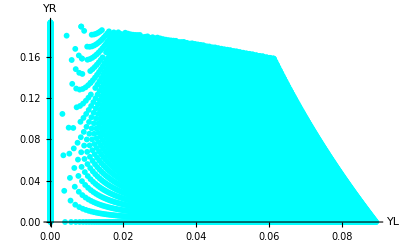

```mathematica
Data0 = Table[If[8 GFSM^2-8 GF^2-(GF^2 x^2)/4≥ 0,{0,x},Null],{x,0,1,0.0001}];
p0=ListPlot[Flatten[{Data,Data0},1],AxesLabel->{"YL","YR"},PlotMarkers->{"●",6},PlotStyle->Cyan]
```

### Plotting

```mathematica
gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
ParametricPlot[Table[{(√YL[Rho,Eta])/GF,(√YR[Rho,Eta])/GF},{Eta,1.0009-0.0014,1.0009+0.0032,0.0001}],{Rho,0.74979-0.00052,0.74979+0.00052}]
```

-Graphics-

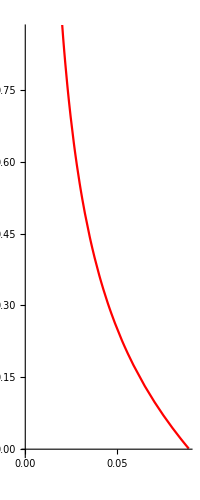

```mathematica
p1=ParametricPlot[{(√YL[Rho,1.0009-0.0014])/GF,(√YR[Rho,1.0009-0.0014])/GF},{Rho,0.74979-0.00052,0.74979+0.000209},PlotStyle->Red]
```

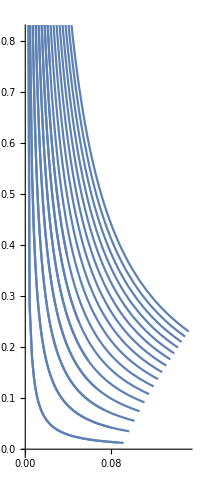

```mathematica
ParametricPlot[Table[{(√YL[Rho,Eta])/GF,(√YR[Rho,Eta])/GF},{Rho,0.74979-0.00052,0.74979+0.00052,0.00002}],{Eta,1.0009-0.0014,1.0009+0.0032}]
```

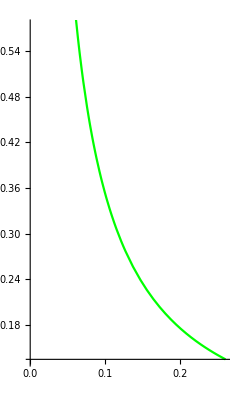

```mathematica
p2=ParametricPlot[{(√YL[0.74979+0.00052,Eta])/GF,(√YR[0.74979+0.00052,Eta])/GF},{Eta,1.0009-0.0042,1.0009+0.0042},PlotStyle->Green]
```

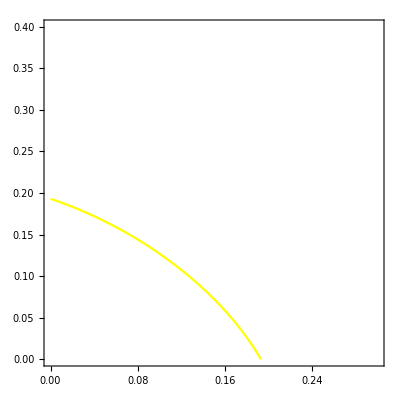

```mathematica
p3 = ContourPlot[128 GFSM^2-(aY[GF^2*x^2,GF^2*y^2]+4bY[GF^2*x^2,GF^2*y^2]+6cY[GF^2*x^2,GF^2*y^2])==0,{x,0,0.3},{y,0,0.4},ContourStyle->Yellow]
```

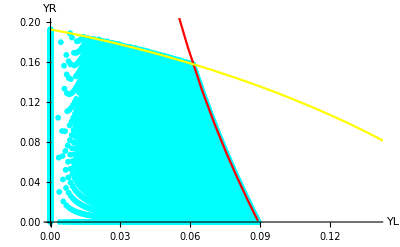

```mathematica
Ylot = Show[{p0,p1,p3},PlotRange->{{0,0.14},{0,0.2}},AxesOrigin->{0,0}]
(*Needs["PlotLegends`"]
ShowLegend[alot,{{{Graphics[{Red,Line[{{0,0},{2,0}}]}],"ξ = 0.9995"},{Graphics[{Green,Line[{{0,0},{2,0}}]}],"ρ = 0.7503"},{Graphics[{Yellow,Line[{{0,0},{2,0}}]}],"G_F = 1.1645*10^-5"}},LegendPosition->{0.7,0.2},LegendSize->{0.75,0.4},LegendShadow->False}]*)
```

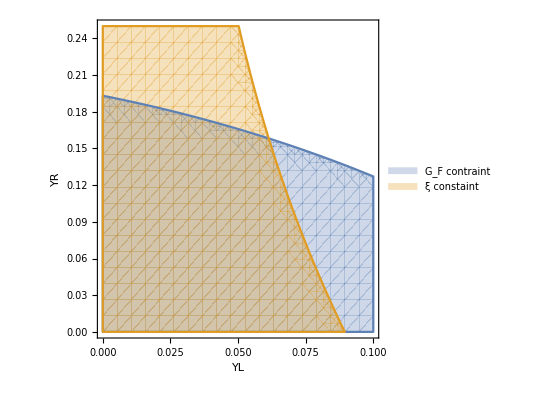

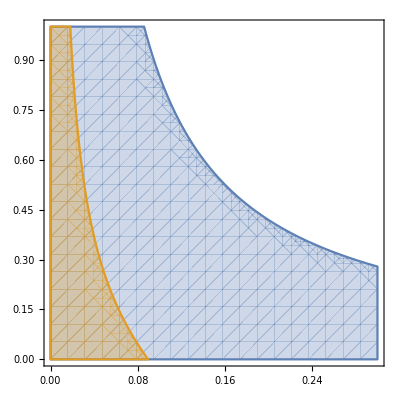

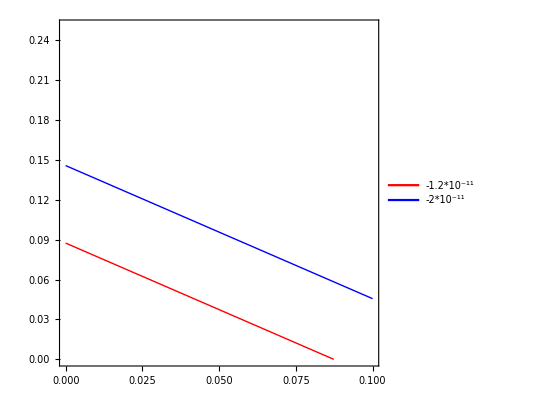

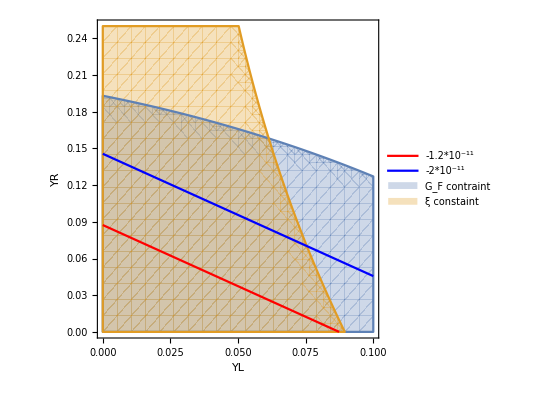

```mathematica
gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
mV = SetPrecision[10,100];
O1 = RegionPlot[{128 GFSM^2-(aY[GF^2*x^2,GF^2*y^2]+4bY[GF^2*x^2,GF^2*y^2]+6cY[GF^2*x^2,GF^2*y^2])≥0 ,1.0041≥(4BY[GF^2*x^2,GF^2*y^2])/(aY[GF^2*x^2,GF^2*y^2]+4bY[GF^2*x^2,GF^2*y^2]+6cY[GF^2*x^2,GF^2*y^2])≥0.9995},{x,0,0.1},{y,0,0.25},FrameLabel->{"YL","YR"},PlotLegends->{"G_F contraint","ξ constaint"}]
RegionPlot[{0.75031
≥(3bY[GF^2*x^2,GF^2*y^2]+6cY[GF^2*x^2,GF^2*y^2])/(aY[GF^2*x^2,GF^2*y^2]+4bY[GF^2*x^2,GF^2*y^2]+6cY[GF^2*x^2,GF^2*y^2]) ≥0.74927,1.0041≥(4BY[GF^2*x^2,GF^2*y^2])/(aY[GF^2*x^2,GF^2*y^2]+4bY[GF^2*x^2,GF^2*y^2]+6cY[GF^2*x^2,GF^2*y^2])≥0.9995},{x,0,0.3},{y,0,1}]
O2=ContourPlot[{YMDM[x*GF*mV^2,y*GF*mV^2,mV,mμ]/(16*Pi^2)==-1.2*10^-11,YMDM[x*GF*mV^2,y*GF*mV^2,mV,mμ]/(16*Pi^2)==-2*10^-11},{x,0,0.1},{y,0,0.25},PlotLegends->Placed[{"-1.2*10^-11","-2*10^-11"},{0.8,0.8}],ContourStyle->{Directive[Red,Thick],Directive[Blue,Thick]}]
Show[O1,O2]
```

### (g-2)_μ contribution

```mathematica
<<X`;(*import package X to calcualate Feynman Functions*)
onShell={p.p->m2^2,p.q->(-q.q)/2,m1->m2,mk->0};
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

```mathematica
(*Form factor*)
Forfactor = "F2";
diagramF1=Table[0,{5}];
(*Diagram a for c1*)
diagramF1[[1]]=e* (-1-Q)*LoopIntegrate[Contract[Spur[(L2*L1*ℙR+R2*R1*ℙL),k.γ,Projector[Forfactor ,μ][{p+q,m1},{p,m2}]](2 Subscript[p, μ]+Subscript[q, μ]-2 Subscript[k, μ])],k,{k,mk},{p-k,mc1},{p+q-k,mc1}]/.onShell;
(*Diagram a for c1*)
diagramF1[[2]]=e *(-1-Q)*mk*LoopIntegrate[Contract[Spur[(L2*R1*ℙR+R2*L1*ℙL),Projector[Forfactor ,μ][{p+q,m1},{p,m2}]](2 Subscript[p, μ]+Subscript[q, μ]-2 Subscript[k, μ])],k,{k,mk},{p-k,mc1},{p+q-k,mc1}]/.onShell;
(*Diagram b for c1*)
diagramF1[[3]]=-e LoopIntegrate[Spur[Subscript[γ, μ],(p+q).γ+m2 𝟙,L2*ℙR+R2*ℙL,k.γ+mk 𝟙,L1*ℙL+R1*ℙR,Projector[Forfactor,μ][{p+q,m1},{p,m2}]] ,k,{k,mk},{p+q,m2},{p+q-k,mc1}]/.onShell;
(*Diagram c for c1*)
diagramF1[[4]]=-e LoopIntegrate[Spur[L2*ℙR+R2*ℙL,k.γ+mk 𝟙,L1*ℙL+R1*ℙR,p.γ+m1 𝟙,Subscript[γ, μ],Projector[Forfactor,μ][{p+q,m1},{p,m2}]] ,k,{k,mk},{p,m1},{p-k,mc1}]/.onShell;
(*Diagram d for c1*)
diagramF1[[5]]=e *Q*LoopIntegrate[Spur[L2*ℙR+R2*ℙL,(p-k).γ+mk 𝟙,Subscript[γ, μ],(p+q-k).γ+mk 𝟙,L1*ℙL+R1*ℙR,Projector[Forfactor,μ][{p+q,m1},{p,m2}]] ,k,{-k+p+q,mk},{k,mc1},{p-k,mk}]/.onShell;
LoopRefine[(Total[diagramF1])/.p.q->0/.Q->0/.q.q->0]//Simplify
```

(e (L1 L2+R1 R2) (m2^4-2 m2^2 mc1^2+(-2 m2^2 mc1^2+2 mc1^4) Log[mc1^2/(-m2^2+mc1^2)]))/(2 m2^4)

```mathematica
Integrate[(1-z-y)/((y+z-1)+a^2),{z,0,1-y},Assumptions->0<y<1&&y∈Reals&&z∈Reals&&a>1]//Simplify
```

-1+y+2 a^2 Log[a]-a^2 Log[-1+a^2+y]

```mathematica
YMDM[YL_,YR_,mc1_,m2_]:=((YL+YR) (m2^4-2 m2^2 mc1^2+(-2 m2^2 mc1^2+2 mc1^4) Log[mc1^2/(-m2^2+mc1^2)]))/(2 m2^4)
```

```mathematica
mV = SetPrecision[10,100];
Data0 = Table[If[8 GFSM^2-8 GF^2-(GF^2 x^2)/4≥ 0,{0,x},Null],{x,0,1,0.0001}];
DataAll = Flatten[{Data,Data0},1];
DataAll=DeleteCases[DataAll,Null,{1}];
NewDataAll=Map[YMDM[#[[1]]*GF*mV^2,#[[2]]*GF*mV^2,mV,mμ]&,DataAll];
NewDataAll=DeleteCases[NewDataAll,_?(Not[NumericQ[#]]&),{1}];
```

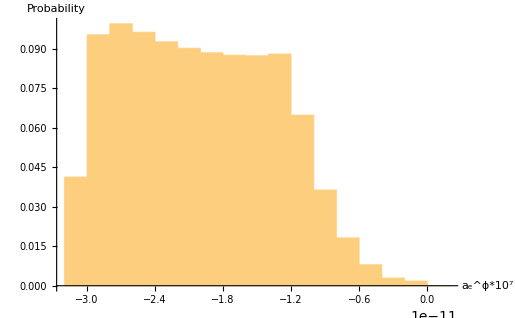

```mathematica
Histogram[NewDataAll/(16*Pi^2),Automatic,"Probability",Axes->{True,True},AxesLabel->{"a_e^ϕ*10^7",Probability}]
```

```mathematica
(*data=Flatten[Table[Map[Insert[#,x,1]&,data],{x,0,1}],1];*)
```

## Bounded Equation for New Vector

```mathematica
(*Defined parameters used in Michel paramter*)(*Forgot the overall 1/16 factor*)
Clear[VL,VR,Rho,Eta,gmW2]
aV[VL_,VR_]:=32(VL*VR);(*Ex: VL = {{|VL|^2}, {mV^2}}*)
AV[VL_,VR_]:=0;
bV[VL_,VR_]:=4*(VR^2+VL^2)+gmW2^2+4*gmW2*VR;(*ReVRr = (Re(VR x Vr^*))/mV^2-> ReVR=(|VR|^2)/mV^2*)
BV[VL_,VR_]:=4*(VR^2-VL^2)+gmW2^2+4*gmW2*VR;
(*Michel paramters for New Vector*)
VRho[VL_,VR_]:=(3bV[VL,VR])/(aV[VL,VR]+4bV[VL,VR])==Rho;
VDelta[VL_,VR_]:=(3BV[VL,VR])/(-3AV[VL,VR]+4BV[VL,VR])==Delta;
VEta[VL_,VR_]:=(-3AV[VL,VR]+4BV[VL,VR])/(aV[VL,VR]+4bV[VL,VR])==Eta;
```

```mathematica
V= Solve[{VRho[VL,VR],VDelta[VL,VR],VEta[VL,VR]},{VL,VR}]//Simplify
```

{{VL→((3 Eta-4 Rho) (gmW2 (3-4 Rho)^2+√(gmW2^2 (3-4 Rho)^2 (-9 Eta^2+16 Rho^2))))/(6 (-3+4 Rho) (-3-3 Eta^2+8 Rho)),VR→-(gmW2 (3-4 Rho)^2+√(gmW2^2 (3-4 Rho)^2 (-9 Eta^2+16 Rho^2)))/(6 (3+3 Eta^2-8 Rho))},{VL→((-3 Eta+4 Rho) (-gmW2 (3-4 Rho)^2+√(gmW2^2 (3-4 Rho)^2 (-9 Eta^2+16 Rho^2))))/(6 (-3+4 Rho) (-3-3 Eta^2+8 Rho)),VR→(-gmW2 (3-4 Rho)^2+√(gmW2^2 (3-4 Rho)^2 (-9 Eta^2+16 Rho^2)))/(6 (3+3 Eta^2-8 Rho))}}

### Plotting

Solution set 1

```mathematica
VL1[Rho_,Eta_]:=Evaluate[VL/.V[[1]]]
VR1[Rho_,Eta_]:=Evaluate[VR/.V[[1]]]
```

```mathematica
gmW2:= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
a = SetPrecision[0.74979+0.00052,100];
b = SetPrecision[1.0009+0.0032,100];
c = SetPrecision[0.74979-0.00052,100];
d = SetPrecision[1.0009-0.0014,100];
f = SetPrecision[0.000001,100];
data1= Flatten[Table[If[Element[VL1[Rho,Eta],Reals]&&Element[VR1[Rho,Eta],Reals]&&VL1[Rho,Eta]≥0&&VR1[Rho,Eta]≥0&& 128 GFSM^2-(aV[VL1[Rho,Eta],VR1[Rho,Eta]]+4bV[VL1[Rho,Eta],VR1[Rho,Eta]])≥0,{VL1[Rho,Eta]/GF,VR1[Rho,Eta]/GF},Null],{Rho,c,a,f},{Eta,d,b,f}],1];
```

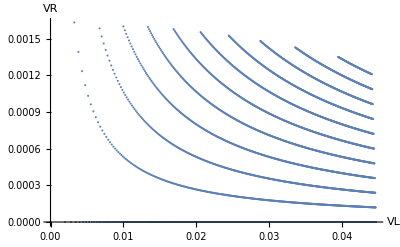

```mathematica
ListPlot[data1,AxesLabel->{"VL","VR"}]
```

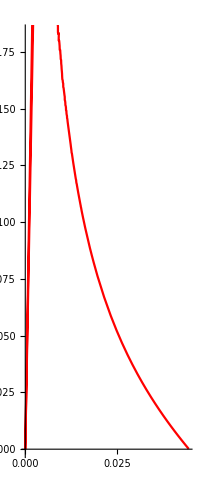

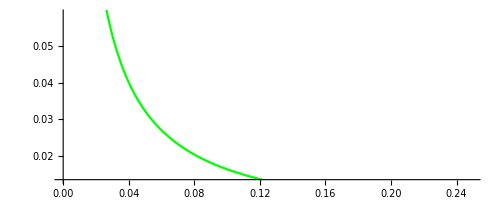

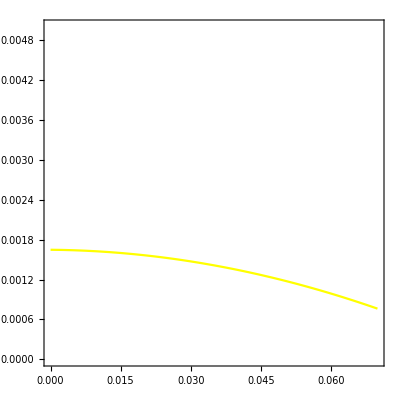

```mathematica
gmW2:= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
g11=ParametricPlot[{VL1[Rho,1.0009-0.0014]/GF,VR1[Rho,1.0009-0.0014]/GF},{Rho,0.74979-0.00052,0.74979+0.000209},PlotStyle->Red]
g21=ParametricPlot[{VL1[0.74979+0.00052,Eta]/GF,VR1[0.74979+0.00052,Eta]/GF},{Eta,1.0009-0.0042,1.0009+0.0042},PlotStyle->Green]
g3 = ContourPlot[128 GFSM^2-(aV[GF*x,GF*y]+4bV[GF*x,GF*y])==0,{x,0,0.07},{y,0,0.005},ContourStyle->Yellow]
```

Solution set 2

```mathematica
VL2[Rho_,Eta_]:=Evaluate[VL/.V[[2]]]
VR2[Rho_,Eta_]:=Evaluate[VR/.V[[2]]]
```

```mathematica
gmW2:= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
data2= Flatten[Table[If[Element[VL2[Rho,Eta],Reals]&&Element[VR2[Rho,Eta],Reals]&&VL2[Rho,Eta]≥0&&VR2[Rho,Eta]≥0&& 128 GFSM^2-(aV[VL2[Rho,Eta],VR2[Rho,Eta]]+4bV[VL2[Rho,Eta],VR2[Rho,Eta]])≥0,{VL2[Rho,Eta]/GF,VR2[Rho,Eta]/GF},Null],{Rho,0.74979-0.00052,0.74979+0.00052,0.000001},{Eta,1.0009-0.0014,1.0009+0.0032,0.000001}],1];
```

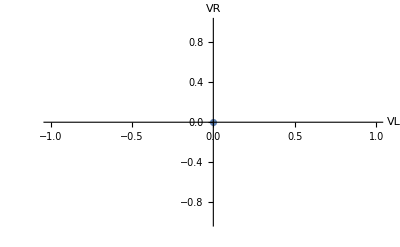

```mathematica
ListPlot[data2,AxesLabel->{"VL","VR"}]
```

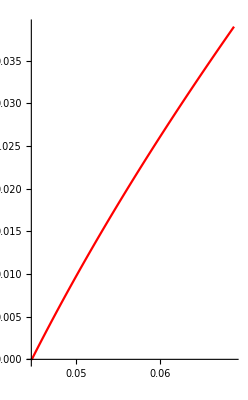

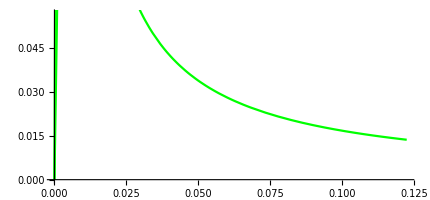

```mathematica
g12=ParametricPlot[{VL2[Rho,1.0009-0.0014]/GF,VR2[Rho,1.0009-0.0014]/GF},{Rho,0.74979-0.00052,0.74979+0.000209},PlotStyle->Red]
g22=ParametricPlot[{VL2[0.74979+0.00052,Eta]/GF,VR2[0.74979+0.00052,Eta]/GF},{Eta,1.0009-0.0042,1.0009+0.0042},PlotStyle->Green]
```

Total solution

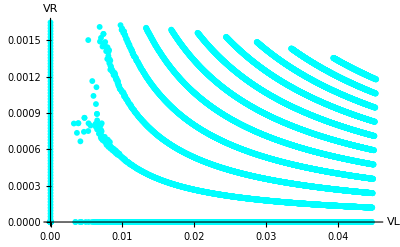

```mathematica
data0 = Table[If[8 GFSM^2-8 GFEW^2≥ 0,{0,Evaluate[VR/.Flatten[Solve[VR^2+gmW2*VR==8 GFSM^2-8 GFEW^2,{VR}],1]]/GF},Null],{GFEW,(1.1661-0.0016)*10^-5,(1.1661+0.0016)*10^-5,0.00001*10^-5}];
g0=ListPlot[Flatten[{data2,data1,data0},1],AxesLabel->{"VL","VR"},PlotMarkers->{"●",6},PlotStyle->Cyan]
```

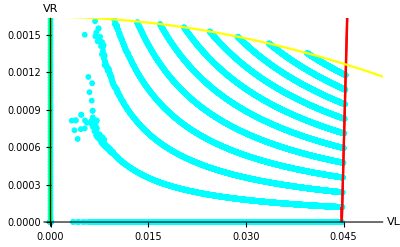

```mathematica
Vlot = Show[{g0,g11,g21,g12,g22,g3},PlotRange->{{0,0.05},{0,0.0016}},AxesOrigin->{0,0}]
```

### (g-2)_μ contribution

```mathematica
<<X`;(*import package X to calcualate Feynman Functions*)
onShell={p.p->m2^2,p.q->(-q.q)/2,m1->m2,mk->0,Q->0};
```

Package-X v2.1.1 already initialized
For more information, see the

```mathematica
(*Form factor*)
Forfactor = "G2";
diagramF2=Table[0,{5}];
(*Diagram a*)
diagramF2[[1]]= e*(1+Q)*LoopIntegrate[Contract[Spur[(L2*ℙL+R2*ℙR),Subscript[γ, μ],k.γ+mk 𝟙,(L1*ℙL+R1*ℙR),Subscript[γ, ν],Projector[Forfactor ,η][{p+q,m1},{p,m2}]](-Subscript[𝕘, μ,λ]+(Subscript[(p-k), μ] Subscript[(p-k), λ])/mW^2)(-Subscript[𝕘, ρ,ν]+(Subscript[(p+q-k), ρ] Subscript[(p+q-k), ν])/mW^2)(Subscript[𝕘, ρ,λ] Subscript[(2p+q-2k), η]-Subscript[𝕘, ρ,η] Subscript[(p+q-k), λ]+Subscript[𝕘, λ,η] Subscript[(k-p), ρ])],k,{k,mk},{p-k,mW},{p+q-k,mW}]/.onShell;
(*Diagram b*)
diagramF2[[2]]=-e LoopIntegrate[Contract[Spur[Subscript[γ, η],(p+q).γ+m2 𝟙,(L2*ℙL+R2*ℙR),Subscript[γ, μ],k.γ+mk 𝟙,(L1*ℙL+R1*ℙR),Subscript[γ, ν],Projector[Forfactor,η][{p+q,m1},{p,m2}]](-Subscript[𝕘, μ,ν]+(Subscript[(p+q-k), μ] Subscript[(p+q-k), ν])/mW^2)] ,k,{k,mk},{p+q,m2},{p+q-k,mW}]/.onShell;
(*Diagram c*)
diagramF2[[3]]=-e LoopIntegrate[Contract[Spur[(L2*ℙL+R2*ℙR),Subscript[γ, μ],k.γ+mk 𝟙,(L1*ℙL+R1*ℙR),Subscript[γ, ν],p.γ+m1 𝟙,Subscript[γ, η],Projector[Forfactor,η][{p+q,m1},{p,m2}]](-Subscript[𝕘, μ,ν]+(Subscript[(p-k), μ] Subscript[(p-k), ν])/mW^2)] ,k,{k,mk},{p,m1},{p-k,mW}]/.onShell;
(*Diagram d*)
diagramF2[[4]]=e *Q*LoopIntegrate[Contract[Spur[(L2*ℙL+R2*ℙR),Subscript[γ, μ],(p-k).γ+mk 𝟙,Subscript[γ, η],(-k+p+q).γ+mk 𝟙,(L1*ℙL+R1*ℙR),Subscript[γ, ν],Projector[Forfactor,η][{p+q,m1},{p,m2}]](-Subscript[𝕘, μ,ν]+(Subscript[(k), μ] Subscript[(k), ν])/mW^2)] ,k,{-k+p,mk},{k,mW},{p+q-k,mk}]/.onShell;
(*Diagram "a"*)
diagramF2[[5]]= e*(1+Q)*LoopIntegrate[Contract[Spur[(L2*ℙL+R2*ℙR),Subscript[γ, μ],k.γ+mk 𝟙,(L1*ℙL+R1*ℙR),Subscript[γ, ν],Projector[Forfactor ,η][{p+q,m1},{p,m2}]](-Subscript[𝕘, μ,λ]+(Subscript[(p-k), μ] Subscript[(p-k), λ])/mW^2)(-Subscript[𝕘, ρ,ν]+(Subscript[(p+q-k), ρ] Subscript[(p+q-k), ν])/mW^2)(-a*Subscript[𝕘, ρ,η] Subscript[(q), λ]+a*Subscript[𝕘, λ,η] Subscript[(q), ρ])],k,{k,mk},{p-k,mW},{p+q-k,mW}]/.onShell;
LoopRefine[(Total[diagramF2])/.p.q->0/.q.q->0/.a->1]//Simplify
```

0

```mathematica
VMDM[VL_,VR_,mW_,m2_]:=((VL+VR) (m2^6+8 m2^4 mW^2-4 m2^2 mW^4+2 (3 m2^4 mW^2-5 m2^2 mW^4+2 mW^6) Log[mW^2/(-m2^2+mW^2)]))/(2 m2^4 mW^2)
```

```mathematica
data0 = Table[If[8 GFSM^2-8 GFEW^2≥ 0,{0,Evaluate[VR/.Flatten[Solve[VR^2+gmW2*VR==8 GFSM^2-8 GFEW^2,{VR}],1]]/GF},Null],{GFEW,(1.1668-0.0011)*10^-5,(1.1668+0.0011)*10^-5,0.00001*10^-5}];
VDataAll = Flatten[{data2,data1,data0},1];
VDataAll=DeleteCases[VDataAll,Null,{1}];
VNewDataAll=Map[VMDM[#[[1]]*GF*10^2,#[[2]]*GF*10^2,10,mμ]&,VDataAll];
VNewDataAll=DeleteCases[VNewDataAll,_?(Not[NumericQ[#]]&),{1}];
```

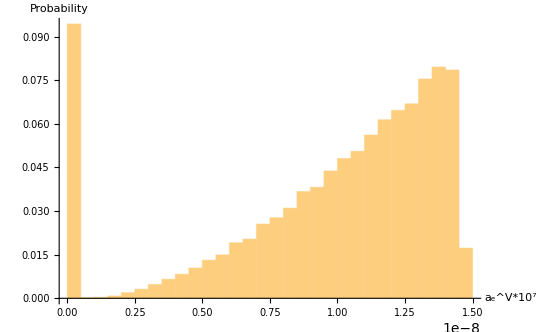

```mathematica
VNewDataAll= VNewDataAll/(16*Pi^2);
Histogram[VNewDataAll*10^7,Automatic,"Probability",Axes->{True,True},AxesLabel->{"a_e^V*10^7",Probability}]
```

```mathematica
(*data=Flatten[Table[Map[Insert[#,x,1]&,data],{x,0,1}],1];*)
```

```mathematica
(*Check SM muon MDM*)
Forfactor = "F2";
diagram=e *Q*LoopIntegrate[Contract[Spur[(L2*ℙL+R2*ℙR),Subscript[γ, μ],(p-k).γ+mk 𝟙,Subscript[γ, η],(-k+p+q).γ+mk 𝟙,(L1*ℙL+R1*ℙR),Subscript[γ, ν],Projector[Forfactor,η][{p+q,m1},{p,m2}]](-Subscript[𝕘, μ,ν])] ,k,{-k+p,mk},{k,0},{p+q-k,mk}]/.{p.p->m2^2,p.q->(-q.q)/2,m1->m2,mk->m2,L1->e,L2->e,R1->e,R2->e};
LoopRefine[diagram/.p.q->0/.q.q->0/.a->1/.Q->-1]//Simplify
```

2 e^3

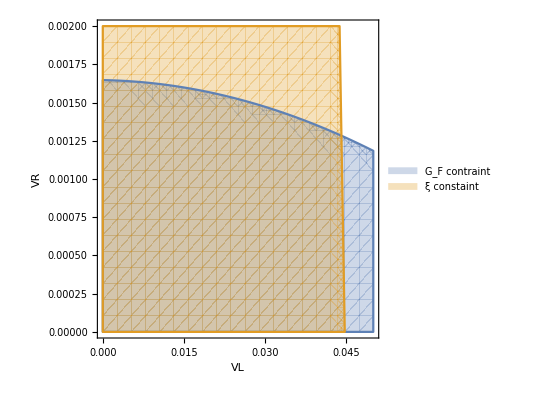

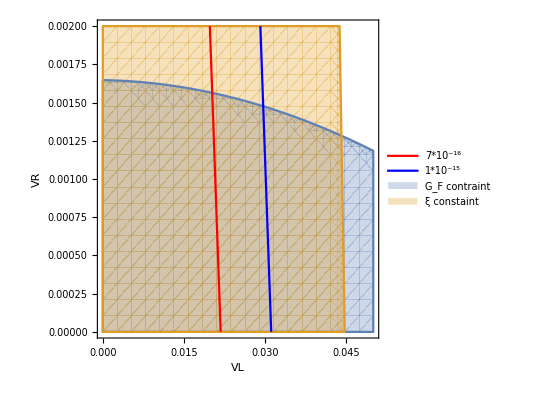

```mathematica
mV = SetPrecision[10,100];
gmW2:= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
O1 = RegionPlot[{128 GFSM^2-(aV[GF*x,GF*y]+4bV[GF*x,GF*y])≥ 0,1.0041≥(4BV[GF*x,GF*y])/(aV[GF*x,GF*y]+4bV[GF*x,GF*y])≥0.9995},{x,0,0.05},{y,0,0.002},FrameLabel->{"VL","VR"},PlotLegends->{"G_F contraint","ξ constaint"}]
O2=ContourPlot[{VMDM[x*GF*mV^2,y*GF*mV^2,mV,mμ]/(16*Pi^2)==7*10^-16,VMDM[x*GF*mV^2,y*GF*mV^2,mV,mμ]/(16*Pi^2)==1*10^-15},{x,0,0.05},{y,0,0.002},PlotLegends->Placed[{"7*10^-16","1*10^-15"},{0.8,0.8}],ContourStyle->{Directive[Red,Thick],Directive[Blue,Thick]}];
Show[O1,O2]
```

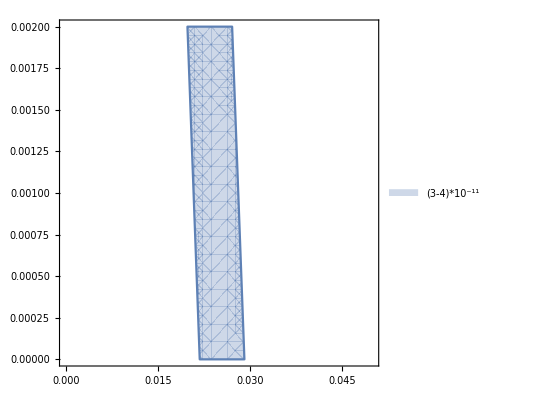

```mathematica
RegionPlot[4*10^-11≥ VMDM[x*GF*mV^2,y*GF*mV^2,mV,mμ]/(16*Pi^2)≥ 3*10^-11,{x,0,0.05},{y,0,0.002},PlotLegends->Placed[{"(3-4)*10^-11"},{0.8,0.8}]]
```

## Bounded Equation for New Scalar (2HDM-like)

```mathematica
(*Defined parameters used in Michel paramter*) (*Forgot the overall 1/16 factor*)
Clear[Rho,Eta,YR,YL,gmW2,mμ,me]
aY[YL_,YR_]:=2*mμ^2*me^2*√(YL*YR);(*Ex: YL = {{|YL|^4}, {mV^4}}*)
AY[YL_,YR_]:=0;
bY[YL_,YR_]:=mμ^2*me^2*YR+mμ^2*me^2*YL+gmW2^2;
BY[YL_,YR_]:=mμ^2*me^2*YR-mμ^2*me^2*YL+gmW2^2;
cY[YL_,YR_]:=1/4*mμ^2*me^2*√(YR*YL);
CY[YL_,YR_]:=0;
(*Michel paramters for New Scalar*)
YRho[YL_,YR_]:=(3bY[YL,YR]+6cY[YL,YR])/(aY[YL,YR]+4bY[YL,YR]+6cY[YL,YR])== Rho;
YDelta[YL_,YR_]:=(3BY[YL,YR]-6CY[YL,YR])/(-3AY[YL,YR]+4BY[YL,YR]-14CY[YL,YR])==Delta;
YEta[YL_,YR_]:=(-3AY[YL,YR]+4BY[YL,YR]-14CY[YL,YR])/(aY[YL,YR]+4bY[YL,YR]+6cY[YL,YR])== Eta;
```

```mathematica
Y = Flatten[Solve[{YRho[YL,YR],YDelta[YL,YR],YEta[YL,YR]},{YL,YR}],1]//Simplify
```

{YL→-(gmW2^2 (12+9 Eta-28 Rho)^2)/(9 (240+9 Eta^2-608 Rho+368 Rho^2)),YR→-(256 gmW2^2 (3-4 Rho)^2)/(9 (240+9 Eta^2-608 Rho+368 Rho^2))}

### Plotting

```mathematica
gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
ParametricPlot[Table[{(√YL[Rho,Eta])/GF,(√YR[Rho,Eta])/GF},{Eta,1.0009-0.0014,1.0009+0.0032,0.0001}],{Rho,0.74979-0.00052,0.74979+0.00052}]
```

-Graphics-

```mathematica
p1=ParametricPlot[{(√YL[Rho,1.0009-0.0014])/GF,(√YR[Rho,1.0009-0.0014])/GF},{Rho,0.74979-0.00052,0.74979+0.000209},PlotStyle->Red]
```

-Graphics-

```mathematica
ParametricPlot[Table[{(√YL[Rho,Eta])/GF,(√YR[Rho,Eta])/GF},{Rho,0.74979-0.00052,0.74979+0.00052,0.00002}],{Eta,1.0009-0.0014,1.0009+0.0032}]
```

-Graphics-

```mathematica
p2=ParametricPlot[{(√YL[0.74979+0.00052,Eta])/GF,(√YR[0.74979+0.00052,Eta])/GF},{Eta,1.0009-0.0042,1.0009+0.0042},PlotStyle->Green]
```

-Graphics-

```mathematica
p3 = ContourPlot[128 GFSM^2-(aY[GF^2*x^2,GF^2*y^2]+4bY[GF^2*x^2,GF^2*y^2]+6cY[GF^2*x^2,GF^2*y^2])==0,{x,0,0.3},{y,0,0.4},ContourStyle->Yellow]
```

-Graphics-

```mathematica
Ylot = Show[{p0,p1,p3},PlotRange->{{0,0.14},{0,0.2}},AxesOrigin->{0,0}]
(*Needs["PlotLegends`"]
ShowLegend[alot,{{{Graphics[{Red,Line[{{0,0},{2,0}}]}],"ξ = 0.9995"},{Graphics[{Green,Line[{{0,0},{2,0}}]}],"ρ = 0.7503"},{Graphics[{Yellow,Line[{{0,0},{2,0}}]}],"G_F = 1.1645*10^-5"}},LegendPosition->{0.7,0.2},LegendSize->{0.75,0.4},LegendShadow->False}]*)
```

-Graphics-

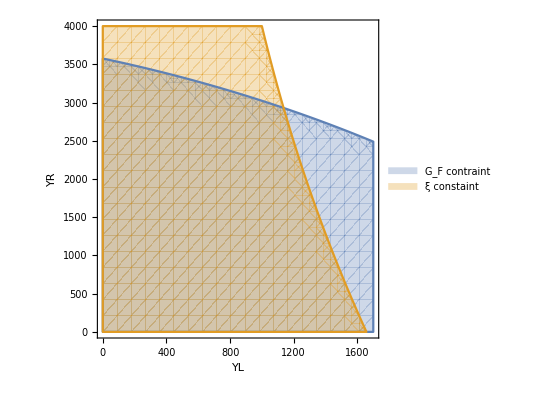

-Graphics-

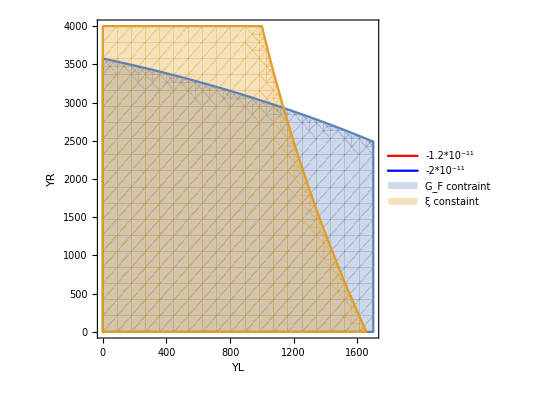

```mathematica
gmW2= SetPrecision[8/(√2)GF,100];(*GF is Fermi constant, gmW2 is g^2/mW^2 where mW is mass of W boson, g is Electroweak SU(2) coupling*)
GF = SetPrecision[1.1657*10^-5,100](*GeV^-2*);
GFSM=SetPrecision[1.1663787*10^-5,100](*GeV^-2*);
mV = SetPrecision[10,100];
mμ=SetPrecision[0.1056583755,100];(*GeV*)
me= SetPrecision[0.00051099895,100];(*GeV*) 
O1 = RegionPlot[{128 GFSM^2-(aY[GF^2*x^2,GF^2*y^2]+4bY[GF^2*x^2,GF^2*y^2]+6cY[GF^2*x^2,GF^2*y^2])≥0 ,1.0041≥(4BY[GF^2*x^2,GF^2*y^2])/(aY[GF^2*x^2,GF^2*y^2]+4bY[GF^2*x^2,GF^2*y^2]+6cY[GF^2*x^2,GF^2*y^2])≥0.9995},{x,0,1700},{y,0,4000},FrameLabel->{"YL","YR"},PlotLegends->{"G_F contraint","ξ constaint"}]
O2=ContourPlot[{YMDM[x*GF*mV^2,y*GF*mV^2,mV,mμ]/(16*Pi^2)==-1.2*10^-11,YMDM[x*GF*mV^2,y*GF*mV^2,mV,mμ]/(16*Pi^2)==-2*10^-11},{x,0,0.1},{y,0,0.25},PlotLegends->Placed[{"-1.2*10^-11","-2*10^-11"},{0.8,0.8}],ContourStyle->{Directive[Red,Thick],Directive[Blue,Thick]}]
Show[O1,O2]
```

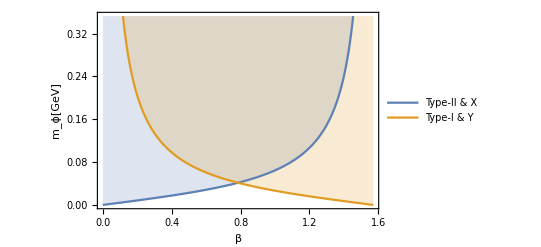

```mathematica
A =Plot[{√((2 √2)/1650)Tan[x],√((2 √2)/1650)Cot[x]},{x,0,Pi/2},Frame->True,FrameLabel->{"β","m_ϕ[GeV]"},Filling->Top, PlotLegends->Placed[LineLegend[{"Type-II & X","Type-I & Y"},LegendFunction->Framed],{0.5,0.5}]]
```

### (g-2)_μ contribution

```mathematica
<<X`;(*import package X to calcualate Feynman Functions*)
onShell={p.p->m2^2,p.q->(-q.q)/2,m1->m2,mk->0};
```

Package-X v2.1.1, by Hiren H. Patel
For more information, see the

```mathematica
(*Form factor*)
Forfactor = "F2";
diagramF1=Table[0,{5}];
(*Diagram a for c1*)
diagramF1[[1]]=e* (-1-Q)*LoopIntegrate[Contract[Spur[(L2*L1*ℙR+R2*R1*ℙL),k.γ,Projector[Forfactor ,μ][{p+q,m1},{p,m2}]](2 Subscript[p, μ]+Subscript[q, μ]-2 Subscript[k, μ])],k,{k,mk},{p-k,mc1},{p+q-k,mc1}]/.onShell;
(*Diagram a for c1*)
diagramF1[[2]]=e *(-1-Q)*mk*LoopIntegrate[Contract[Spur[(L2*R1*ℙR+R2*L1*ℙL),Projector[Forfactor ,μ][{p+q,m1},{p,m2}]](2 Subscript[p, μ]+Subscript[q, μ]-2 Subscript[k, μ])],k,{k,mk},{p-k,mc1},{p+q-k,mc1}]/.onShell;
(*Diagram b for c1*)
diagramF1[[3]]=-e LoopIntegrate[Spur[Subscript[γ, μ],(p+q).γ+m2 𝟙,L2*ℙR+R2*ℙL,k.γ+mk 𝟙,L1*ℙL+R1*ℙR,Projector[Forfactor,μ][{p+q,m1},{p,m2}]] ,k,{k,mk},{p+q,m2},{p+q-k,mc1}]/.onShell;
(*Diagram c for c1*)
diagramF1[[4]]=-e LoopIntegrate[Spur[L2*ℙR+R2*ℙL,k.γ+mk 𝟙,L1*ℙL+R1*ℙR,p.γ+m1 𝟙,Subscript[γ, μ],Projector[Forfactor,μ][{p+q,m1},{p,m2}]] ,k,{k,mk},{p,m1},{p-k,mc1}]/.onShell;
(*Diagram d for c1*)
diagramF1[[5]]=e *Q*LoopIntegrate[Spur[L2*ℙR+R2*ℙL,(p-k).γ+mk 𝟙,Subscript[γ, μ],(p+q-k).γ+mk 𝟙,L1*ℙL+R1*ℙR,Projector[Forfactor,μ][{p+q,m1},{p,m2}]] ,k,{-k+p+q,mk},{k,mc1},{p-k,mk}]/.onShell;
LoopRefine[(Total[diagramF1])/.p.q->0/.Q->0/.q.q->0]//Simplify
```

(e (L1 L2+R1 R2) (m2^4-2 m2^2 mc1^2+(-2 m2^2 mc1^2+2 mc1^4) Log[mc1^2/(-m2^2+mc1^2)]))/(2 m2^4)

```mathematica
Integrate[(1-z-y)/((y+z-1)+a^2),{z,0,1-y},Assumptions->0<y<1&&y∈Reals&&z∈Reals&&a>1]//Simplify
```

-1+y+2 a^2 Log[a]-a^2 Log[-1+a^2+y]

```mathematica
YMDM[YL_,YR_,mc1_,m2_]:=((YL+YR) (m2^4-2 m2^2 mc1^2+(-2 m2^2 mc1^2+2 mc1^4) Log[mc1^2/(-m2^2+mc1^2)]))/(2 m2^4)
```

```mathematica
mV = SetPrecision[10,100];
Data0 = Table[If[8 GFSM^2-8 GF^2-(GF^2 x^2)/4≥ 0,{0,x},Null],{x,0,1,0.0001}];
DataAll = Flatten[{Data,Data0},1];
DataAll=DeleteCases[DataAll,Null,{1}];
NewDataAll=Map[YMDM[#[[1]]*GF*mV^2,#[[2]]*GF*mV^2,mV,mμ]&,DataAll];
NewDataAll=DeleteCases[NewDataAll,_?(Not[NumericQ[#]]&),{1}];
```

```mathematica
Histogram[NewDataAll/(16*Pi^2),Automatic,"Probability",Axes->{True,True},AxesLabel->{"a_e^ϕ*10^7",Probability}]
```

-Graphics-

```mathematica
(*data=Flatten[Table[Map[Insert[#,x,1]&,data],{x,0,1}],1];*)
```